```mathematica
SetDirectory["D:\\Life and Science\\Summer 2024\\Heun\\DataSets"]
```

D:\Life and Science\Summer 2024\Heun\DataSets

```mathematica
a[A_,B_,ω_][t_]:=B+A*Cos[ω*t];
h[A_,B_,ω_][t_]:=1/2*(a[A,B,ω][t]-1.);
f[A_,B_,ω_][t_]:=1/2*(a[A,B,ω][t]+1.);
f2der[A_,B_,ω_][t_]:=D[f[A,B,ω][z],{z,2}]/.{z->t}
f1der[A_,B_,ω_][t_]:=D[f[A,B,ω][z],z]/.{z->t}
```

```mathematica
V[A_,B_,ω_][t_]:=-f[A,B,ω][t]*h[A,B,ω][t]+3/4*f1der[A,B,ω][t]^2/f[A,B,ω][t]^2-1/2*f2der[A,B,ω][t]/f[A,B,ω][t];
V[A,B,ω][t]//FullSimplify
```

1/4 ((2 A ω^2 Cos[t ω])/(1.+B+A Cos[t ω])-1. (-1.+B+A Cos[t ω]) (1.+B+A Cos[t ω])+(3 A^2 ω^2 Sin[t ω]^2)/(1.+B+A Cos[t ω])^2)

```mathematica
HillPotential[A_,B_,ω_][t_]:=1/(4 (1+B+A Cos[t ω])^2)(2 A ω^2 Cos[t ω] (1+B+A Cos[t ω])-(-1+B+A Cos[t ω]) (1+B+A Cos[t ω])^3+3 A^2 ω^2 Sin[t ω]^2);
FunctionPeriod[1/(4 (1+B+A Cos[t ω])^2)(2 A ω^2 Cos[t ω] (1+B+A Cos[t ω])-(-1+B+A Cos[t ω]) (1+B+A Cos[t ω])^3+3 A^2 ω^2 Sin[t ω]^2),t]
```

(2 π)/ω

```mathematica
Integrate[HillPotential[A,B,ω][t]-1/4*B^2,{t,0,2*Pi/ω},Assumptions->{A>0,B>0,A<B+1,ω>0}]
```

(π (2-A^2-4 B^2+(2 B ω^2)/(√(-A^2+(1+B)^2))+2 (-1+1/(√(-A^2+(1+B)^2))) ω^2))/(4 ω)

```mathematica
(π (2-A^2-4 B^2+(2 B ω^2)/(√(-A^2+(1+B)^2))+2 (-1+1/(√(-A^2+(1+B)^2))) ω^2))/(4 ω)//FullSimplify
```

(π (2-A^2-4 B^2+(2 B ω^2)/(√(-A^2+(1+B)^2))+2 (-1+1/(√(-A^2+(1+B)^2))) ω^2))/(4 ω)

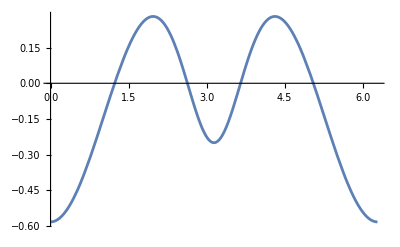

```mathematica
Plot[HillPotential[1.,1.,1.][t],{t,0,2*Pi},PlotRange->All]
```

```mathematica
AMatrix[A_,B_,ω_][t_]:={{0,1},{HillPotential[A,B,ω][t],0}};
DAAMatrix[A_,B_,ω_][t_]:=D[AMatrix[z,B,ω][t],z]/.{z->A};
DBAMatrix[A_,B_,ω_][t_]:=D[AMatrix[A,z,ω][t],z]/.{z->B};
```

```mathematica
TTMatrixRHS=Flatten[AMatrix[A,B,ω][t].{{tt[1][t],tt[2][t]},{tt[3][t],tt[4][t]}}];
TTMatrixEqs=Join[Table[D[tt[i][t],t]==TTMatrixRHS[[i]],{i,Length[TTMatrixRHS]}],{tt[1][0]==1,tt[2][0]==0,tt[3][0]==0,tt[4][0]==1}];
TTAMatrixRHS=Flatten[AMatrix[A,B,ω][t].{{tta[1][t],tta[2][t]},{tta[3][t],tta[4][t]}}+DAAMatrix[A,B,ω][t].{{tt[1][t],tt[2][t]},{tt[3][t],tt[4][t]}}];
TTAMatrixEqs=Join[Table[D[tta[i][t],t]==TTAMatrixRHS[[i]],{i,Length[TTAMatrixRHS]}],{tta[1][0]==0,tta[2][0]==0,tta[3][0]==0,tta[4][0]==0}];
TTBMatrixRHS=Flatten[AMatrix[A,B,ω][t].{{ttb[1][t],ttb[2][t]},{ttb[3][t],ttb[4][t]}}+DBAMatrix[A,B,ω][t].{{tt[1][t],tt[2][t]},{tt[3][t],tt[4][t]}}];
TTBMatrixhEqs=Join[Table[D[ttb[i][t],t]==TTBMatrixRHS[[i]],{i,Length[TTBMatrixRHS]}],{ttb[1][0]==0,ttb[2][0]==0,ttb[3][0]==0,ttb[4][0]==0}];
```

```mathematica
fullSet=Join[TTMatrixEqs,TTAMatrixEqs,TTBMatrixhEqs];
variables=Join[Table[tt[i][t],{i,1,4}],Table[tta[i][t],{i,1,4}],Table[ttb[i][t],{i,1,4}]];
```

```mathematica
A=1.;B=1.;ω=1.;
```

```mathematica
TTAtest=Table[tta[i][t],{i,1,4}]/.NDSolve[fullSet,variables,{t,0,2*Pi}][[1]];
TTBtest=Table[ttb[i][t],{i,1,4}]/.NDSolve[fullSet,variables,{t,0,2*Pi}][[1]];
TTAMatrixTest[z_]:={{TTAtest[[1]],TTAtest[[2]]},{TTAtest[[3]],TTAtest[[4]]}}/.{t->z};
TTBMatrixTest[z_]:={{TTBtest[[1]],TTBtest[[2]]},{TTBtest[[3]],TTBtest[[4]]}}/.{t->z};
```

```mathematica
Tr[TTAMatrixTest[2*Pi]]/Tr[TTBMatrixTest[2*Pi]]
```

0.44639